```mathematica
data={{495.8,228.33,-182.71, 256.04,
-291.19, 288.93,-300.92},
{490.2, 227.84,-184.16, 259.14,
-285.11, 280.96,-306.65},
{536.2, 230.05,-183.98, 259.16,
-294.65, 290.38,-308.54},
{533.6, 229.57,-182.49, 260.88,
-288.64, 294.04,-307.43},
{578.6, 232.26,-185.01, 263.25,
-297.07, 298.15,-314.52},
{591.8, 233.54,-188.25, 274.71,
-289.44, 296.00,-314.12},
{643.2, 235.98,-188.13, 272.80,
-298.56, 297.02,-321.13},
{643.2, 236.84,-189.49, 274.57,
-292.33, 297.70,-317.05},
{695.2, 238.01,-188.61, 272.52,
-292.27, 301.66,-320.98},
{695.5, 238.35,-188.73, 273.09,
-293.86, 297.88,-319.52},
{746.4, 239.86,-191.02, 273.65,
-292.00, 304.40,-323.96},
{746.1, 242.77,-188.11, 276.88,
-293.57, 305.06,-323.85},
{800.3, 246.55,-185.25, 273.61,
-292.74, 306.64,-325.82},
{798.0, 244.95,-191.62, 278.82,
-296.60, 309.79,-329.02},
{850.4, 249.22,-193.76, 283.26,
-301.24, 320.29,-330.22}
};
```

```mathematica
DA=Transpose[data]
```

{{495.8,490.2,536.2,533.6,578.6,591.8,643.2,643.2,695.2,695.5,746.4,746.1,800.3,798.,850.4},{228.33,227.84,230.05,229.57,232.26,233.54,235.98,236.84,238.01,238.35,239.86,242.77,246.55,244.95,249.22},{-182.71,-184.16,-183.98,-182.49,-185.01,-188.25,-188.13,-189.49,-188.61,-188.73,-191.02,-188.11,-185.25,-191.62,-193.76},{256.04,259.14,259.16,260.88,263.25,274.71,272.8,274.57,272.52,273.09,273.65,276.88,273.61,278.82,283.26},{-291.19,-285.11,-294.65,-288.64,-297.07,-289.44,-298.56,-292.33,-292.27,-293.86,-292.,-293.57,-292.74,-296.6,-301.24},{288.93,280.96,290.38,294.04,298.15,296.,297.02,297.7,301.66,297.88,304.4,305.06,306.64,309.79,320.29},{-300.92,-306.65,-308.54,-307.43,-314.52,-314.12,-321.13,-317.05,-320.98,-319.52,-323.96,-323.85,-325.82,-329.02,-330.22}}

```mathematica
TableForm[DA]
```

495.8 | 490.2 | 536.2 | 533.6 | 578.6 | 591.8 | 643.2 | 643.2 | 695.2 | 695.5 | 746.4 | 746.1 | 800.3 | 798. | 850.4
228.33 | 227.84 | 230.05 | 229.57 | 232.26 | 233.54 | 235.98 | 236.84 | 238.01 | 238.35 | 239.86 | 242.77 | 246.55 | 244.95 | 249.22
-182.71 | -184.16 | -183.98 | -182.49 | -185.01 | -188.25 | -188.13 | -189.49 | -188.61 | -188.73 | -191.02 | -188.11 | -185.25 | -191.62 | -193.76
256.04 | 259.14 | 259.16 | 260.88 | 263.25 | 274.71 | 272.8 | 274.57 | 272.52 | 273.09 | 273.65 | 276.88 | 273.61 | 278.82 | 283.26
-291.19 | -285.11 | -294.65 | -288.64 | -297.07 | -289.44 | -298.56 | -292.33 | -292.27 | -293.86 | -292. | -293.57 | -292.74 | -296.6 | -301.24
288.93 | 280.96 | 290.38 | 294.04 | 298.15 | 296. | 297.02 | 297.7 | 301.66 | 297.88 | 304.4 | 305.06 | 306.64 | 309.79 | 320.29
-300.92 | -306.65 | -308.54 | -307.43 | -314.52 | -314.12 | -321.13 | -317.05 | -320.98 | -319.52 | -323.96 | -323.85 | -325.82 | -329.02 | -330.22

```mathematica
Ec=(DA[[2]]+Abs[DA[[3]]])/2;
Pr=(DA[[4]]+Abs[DA[[5]]])/2;
Ps=(DA[[6]]+Abs[DA[[7]]])/2;
EcV=Transpose[{DA[[1]],Ec}];
PrV=Transpose[{DA[[1]],Pr}];
PsV=Transpose[{DA[[1]],Ps}];
lmEc=LinearModelFit[EcV,x,x];
lmPr=LinearModelFit[PrV,x,x];
lmPs=LinearModelFit[PsV,x,x];
```

0.958622

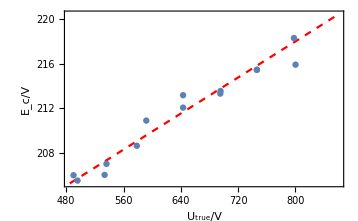

```mathematica
lmEc["RSquared"]
Show[
Plot[lmEc[x],{x,485,860},PlotStyle->{Dashed,Red},PlotLegends->Placed[{"线性拟合"},{Left,Top}]],
ListPlot[EcV,PlotLegends->Placed[{"数据点"},{Left,Top}]],
AxesLabel->{"U_true/V","E_c/V"},
Frame->True,Grid->Automatic]
```

0.796473

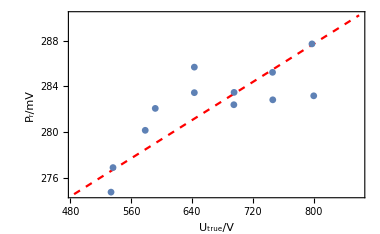

```mathematica
lmPr["RSquared"]
Show[
Plot[lmPr[x],{x,485,860},PlotStyle->{Dashed,Red},PlotLegends->Placed[{"线性拟合"},{Left,Top}]],
ListPlot[PrV,PlotLegends->Placed[{"数据点"},{Left,Top}]],
AxesLabel->{"U_true/V","P_r/mV"},
Frame->True]
```

0.953841

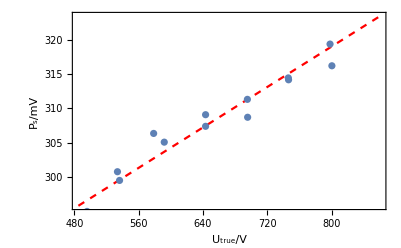

```mathematica
lmPs["RSquared"]
Show[
Plot[lmPs[x],{x,485,860},PlotStyle->{Dashed,Red},PlotLegends->Placed[{"线性拟合"},{Left,Top}]],
ListPlot[PsV,PlotLegends->Placed[{"数据点"},{Left,Top}]],
AxesLabel->{"U_true/V","P_s/mV"},
Frame->True]
```